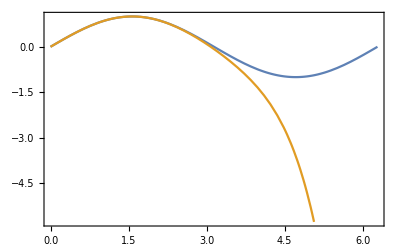
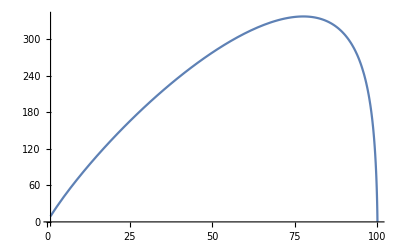
```mathematica
<<MaTeX`
MaTeX["x^2"]
-Graphics-
ConfigureMaTeX["pdfLaTeX"->"C:\\Users\\Musto Family\\AppData\\Local\\Programs\\MiKTeX 2.9\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs9.50\\bin\\gswin64c.exe"]

funs={Sin[x],Normal[Sin[x]+O[x]^8]};

Plot[Evaluate[funs],{x,0,2 Pi},PlotLegends->MaTeX/@funs,BaseStyle->{FontFamily->"Times"},Frame->True,FrameStyle->BlackFrame]
{"CacheSize"->100,"WorkingDirectory"->Automatic,"pdfLaTeX"->"C:\\Users\\Musto Family\\AppData\\Local\\Programs\\MiKTeX 2.9\\miktex\\bin\\x64\\pdflatex.exe","Ghostscript"->"C:\\Program Files\\gs\\gs9.50\\bin\\gswin64c.exe"}
-Graphics-
Entrocom2[ i_,cra_, Leng_]:= Log[ (     (Leng-i*cra + i)! ) / ((Leng-i*cra)! * i! )] 
texStyle={FontFamily->"LM Roman 12",FontSize->20};
Plot[{Entrocom2[x,100,10000]},{x,1,100},AxesLabel->MaTeX[{"n"," \\log \\Omega"},Magnification->1.8],PlotLegends->MaTeX[{"\\textrm{Exact}","\\textrm{Approximated}"," k =2", "k=1"}, Magnification->1.8],BaseStyle->texStyle]
-Graphics-
```

-Graphics-

-Graphics-

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Users\Musto Family\AppData\Local\Programs\MiKTeX 2.9\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs9.50\bin\gswin64c.exe}

-Graphics-

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Users\Musto Family\AppData\Local\Programs\MiKTeX 2.9\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs9.50\bin\gswin64c.exe}

-Graphics-

-Graphics-

-Graphics-

```mathematica
J1[delta_,w_]:=(4*((delta/(w+2^(1/6)*delta))^12-(delta/(w+2^(1/6)*delta))^6)+1) - w
U[x_]:=J1[1/10,x]
Uder[s_]:=D[U[x],{x,2}]/.x->s;
U1[x_]:=J1[1/100,x]
Uder1[s_]:=D[U1[x],{x,2}]/.x->s;
U2[x_]:=J1[1/500,x]
Uder2[s_]:=D[U2[x],{x,2}]/.x->s;
```

```mathematica
max=NMaximize[{-U[w],0≤w<1/2},{w},Method->"NelderMead",WorkingPrecision->150,AccuracyGoal->150];
turn=w/.NSolve[{-U[w]==max[[1]],1/2≤w},w,Reals,WorkingPrecision->150][[1]][[1]];L=4;
max1=NMaximize[{-U1[w],0≤w<1/2},{w},Method->"NelderMead",WorkingPrecision->150,AccuracyGoal->150];
turn1=w/.NSolve[{-U1[w]==max1[[1]],1/2≤w},w,Reals,WorkingPrecision->150][[1]][[1]];
max2=NMaximize[{-U2[w],0≤w<1/10},{w},Method->"NelderMead",WorkingPrecision->150,AccuracyGoal->150];
turn2=w/.NSolve[{-U2[w]==max2[[1]],1/2≤w},w,Reals,WorkingPrecision->150][[1]][[1]];

U[0.01]//N
U1[0.01]//N
turn
turn1
```

0.15059

0.946724

1.00008635478651790136185534423731817932533693773334859529023934218047292313441305609092828967874113470701753499972608724953292077043888909572050231588

1.00000087589793580658134350242272961258656442172336345779325949733561052834313081155351589567376552052730829077847011324917968467969036311995222100795

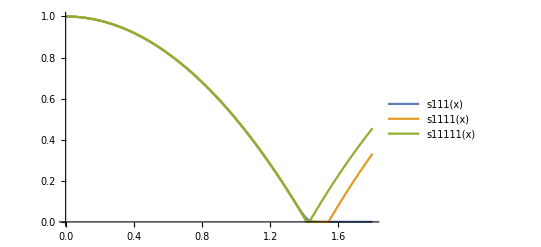

```mathematica
s111=NDSolveValue[{y''[x]-U'[y[x]]==0,y[0]==turn,y'[0]==0},y,{x,0,L},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->8,"PositionVariables"->{y[x]}},StartingStepSize->1/10000,WorkingPrecision->30,MaxSteps->Infinity];
s1111=NDSolveValue[{y''[x]-U1'[y[x]]==0,y[0]==turn1,y'[0]==0},y,{x,0,L},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->8,"PositionVariables"->{y[x]}},StartingStepSize->1/10000,WorkingPrecision->30,MaxSteps->Infinity];
s11111=NDSolveValue[{y''[x]-U2'[y[x]]==0,y[0]==turn2,y'[0]==0},y,{x,0,L},Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->8,"PositionVariables"->{y[x]}},StartingStepSize->1/10000,WorkingPrecision->30,MaxSteps->Infinity];
zerof[x]:=0


Plot[{s111[x], s1111[x],s11111[x]},{x,0,1.8}, PlotLegends->"Expressions"]
```

ParametricFunction[<>]

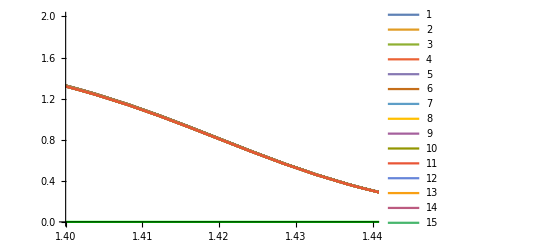

```mathematica
pfun4=ParametricNDSolveValue[{ -y''[x]+Uder[(s111[x])]*y[x]==Ei*y[x],y[0]==1,y'[0]==0},y,{x,0,L},{Ei}]
Show[Plot[{U[x],zerof[x]},{x,1.4,1.6},PlotStyle->Directive[Thick,Green]],Plot[Evaluate@Table[Re[pfun4[Ei][x]],{Ei,-2*0.365,-2*0.36,0.0001}],{x,1.4,1.6},PlotLegends->Automatic],PlotRange->{{1.4,1.44},{0,2}}]
```

ParametricFunction[<>]

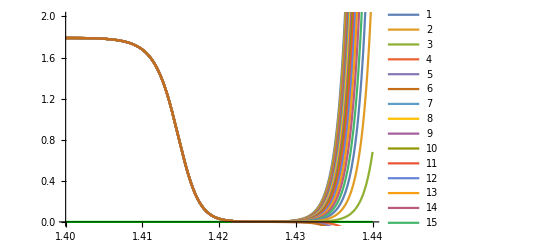

```mathematica
pfun5=ParametricNDSolveValue[{ -y''[x]+Uder1[(s1111[x])]*y[x]==Ei*y[x],y[0]==1,y'[0]==0},y,{x,0,L},{Ei}]
Show[Plot[{U1[x],zerof[x]},{x,1.4,1.44},PlotStyle->Directive[Thick,Green]],Plot[Evaluate@Table[Re[pfun5[Ei][x]],{Ei,-2*0.3607,-2*0.3606,0.00001}],{x,1.4,1.44},PlotLegends->Automatic],PlotRange->{{1.4,1.44},{0,2}}]
```

ParametricFunction[<>]

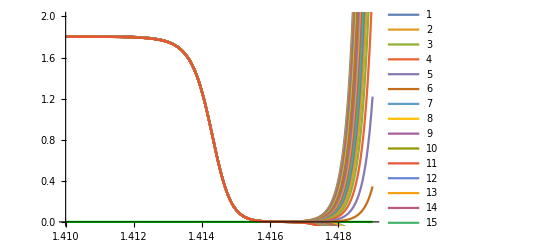

```mathematica
pfun6=ParametricNDSolveValue[{ -y''[x]+Uder2[(s11111[x])]*y[x]==Ei*y[x],y[0]==1,y'[0]==0},y,{x,0,L},{Ei}]
Show[Plot[{U2[x],zerof[x]},{x,1.41,1.419},PlotStyle->Directive[Thick,Green]],Plot[Evaluate@Table[Re[pfun6[Ei][x]],{Ei,-2*0.361,-2*0.359,0.0001}],{x,1.41,1.419},PlotLegends->Automatic],PlotRange->{{1.41,1.419},{0.,2}}]
```

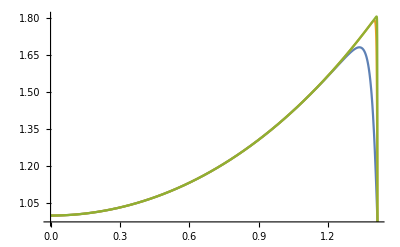

```mathematica
Plot[{pfun4[-2*0.3601][x],pfun5[-2*0.3601][x],pfun6[-2*0.3601][x]},{x,0,Sqrt[2]}]
```

ParametricFunction[<>]

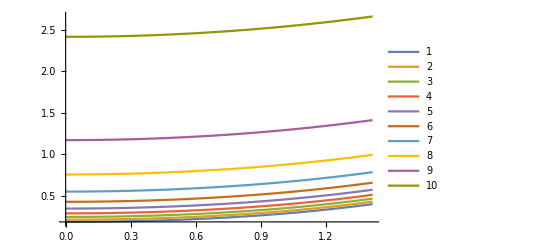

```mathematica
pfunfin=ParametricNDSolveValue[{ -y''[x]==Ei*y[x],y'[0]==0,y'[Sqrt[2]]==(Sqrt[2]-1/Sqrt[2])/2},y,{x,0,Sqrt[2]},{Ei}]
Show[Plot[Evaluate@Table[Re[pfunfin[Ei][x]],{Ei,-1,-0.1,0.1}],{x,0,Sqrt[2]},PlotLegends->Automatic],PlotRange->All]
```

```mathematica
pfuplo[x_]:=Piecewise[{{pfunfin[-2*0.359807][x], x< Sqrt[2]},{0, x> Sqrt[2]}}]
```

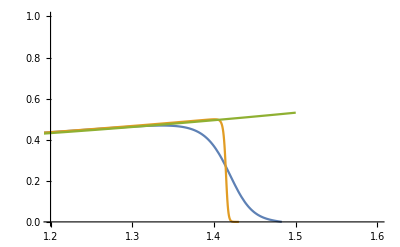

```mathematica
Plot[{(1.01)*(pfunfin[-2*0.359807][0])*pfun4[-2*0.360613][x],(1.01)*(pfunfin[-2*0.359807][0])*pfun5[-2*0.360613][x],pfunfin[-2*0.359807][x]},{x,0,1.5}, PlotRange->{{1.2,1.6},{0,1}}]
```

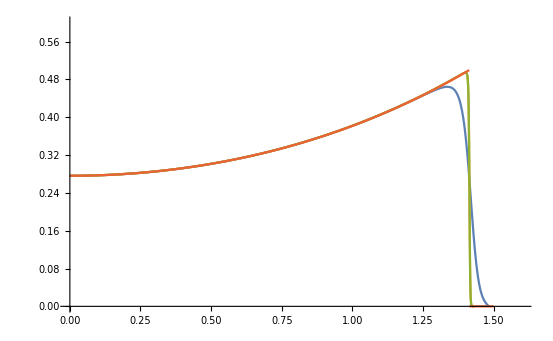

```mathematica
Plot[{(1.0)*(pfuplo[0])*pfun4[-2*0.360613][x],(1.0)*(pfuplo[0])*pfun5[-2*0.360613][x],(1.0)*(pfuplo[0])*pfun5[-2*0.360613][x],pfuplo[x]},{x,0,1.5}, PlotRange->{{0,1.6},{0,0.6}}]
```

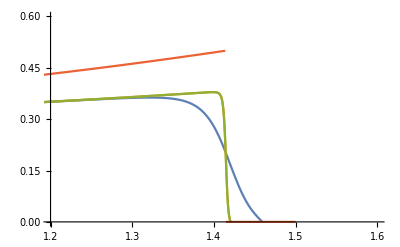

```mathematica
Plot[{(1.0)*(pfuplo[0])*pfun4[-0.360613][x],(1.0)*(pfuplo[0])*pfun5[-0.360613][x],(1.0)*(pfuplo[0])*pfun5[-0.360613][x],pfuplo[x]},{x,0,1.5}, PlotRange->{{1.2,1.6},{0,0.6}}]
```

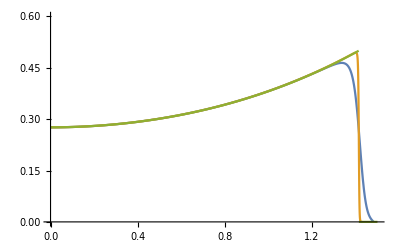

```mathematica
Plot[{{(1.0)*(pfuplo[0])*pfun4[-2*0.360613][x],(1.0)*(pfuplo[0])*pfun5[-2*0.360613][x],pfuplo[x]}},{x,0,1.5},PlotRange->{{0,1.5},{0,0.6}},AxesLabel->MaTeX[{"x"," w(x)"},Magnification->1.8],PlotLegends->MaTeX[{"\\zeta = 0.1","\\zeta = 0.01", "\\textrm{Analytical}"}, Magnification->1.8],BaseStyle->texStyle]
```

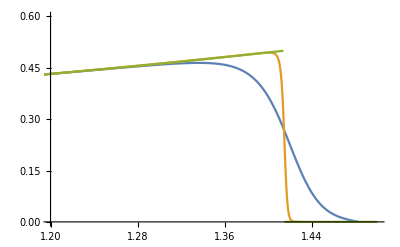

```mathematica
Plot[{{(1.0)*(pfuplo[0])*pfun4[-2*0.360613][x],(1.0)*(pfuplo[0])*pfun5[-2*0.360613][x],pfuplo[x]}},{x,0,1.5},PlotRange->{{1.2,1.5},{0,0.6}},AxesLabel->MaTeX[{"x"," w(x)"},Magnification->1.8],PlotLegends->MaTeX[{"\\zeta = 0.1","\\zeta = 0.01", "\\textrm{Analytical}"}, Magnification->1.8],BaseStyle->texStyle]
```

```mathematica
Export["Eigenfunctions.pdf", Plot[{{(1.0)*(pfuplo[0])*pfun4[-2*0.360613][x],(1.0)*(pfuplo[0])*pfun5[-2*0.360613][x],pfuplo[x]}},{x,0,1.5},PlotRange->{{1.2,1.5},{0,0.6}},AxesLabel->MaTeX[{"x"," w(x)"},Magnification->1.8],PlotLegends->MaTeX[{"\\zeta = 0.1","\\zeta = 0.01", "\\textrm{Analytical}"}, Magnification->1.8],BaseStyle->texStyle]]
```

Eigenfunctions.pdf

```mathematica
Export["Eigenfunctions_full.pdf", Plot[{{(1.0)*(pfuplo[0])*pfun4[-2*0.360613][x],(1.0)*(pfuplo[0])*pfun5[-2*0.360613][x],pfuplo[x]}},{x,0,1.5},PlotRange->{{0,1.5},{0,0.6}},AxesLabel->MaTeX[{"x"," w(x)"},Magnification->1.8],PlotLegends->MaTeX[{"\\zeta = 0.1","\\zeta = 0.01", "\\textrm{Analytical}"}, Magnification->1.8],BaseStyle->texStyle]]
```

Eigenfunctions_full.pdf

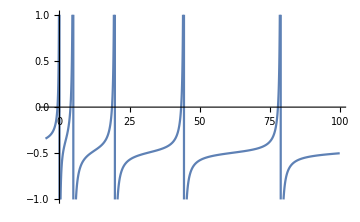

```mathematica
Plot[pfunfin[Ei][Sqrt[2]]-0.5,{Ei,-5,100},ImageSize->Medium, PlotRange->{{-5,100},{-1,1}}]
```

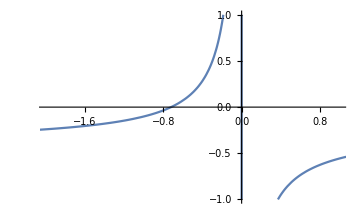

```mathematica
Plot[pfunfin[Ei][Sqrt[2]]-0.5,{Ei,-5,10},ImageSize->Medium, PlotRange->{{-2,1},{-1,1}},AxesLabel->MaTeX[{"\\epsilon"," w(x ; \\epsilon)"}, Magnification->1.8],BaseStyle->texStyle]
```

```mathematica
Export["spectrum_neg.pdf", Plot[pfunfin[Ei][Sqrt[2]]-0.5,{Ei,-5,100},ImageSize->Medium, PlotRange->{{-2,1},{-1,1}},AxesLabel->MaTeX[{"\\epsilon"," w(x ; \\epsilon)"}, Magnification->1.8],BaseStyle->texStyle]]
```

spectrum_neg.pdf

```mathematica
ptest[x_]:=pfunfin[x][Sqrt[2]]
```

```mathematica
(*Plot[pfunfin[Ei][Sqrt[2]]-0.5,{Ei,-5,100},Exclusions->{(pfunfin[Ei][Sqrt[2]]-pfunfin[Ei+0.1][Sqrt[2]])/.1==10,(pfunfin[Ei][Sqrt[2]]-pfunfin[Ei+0.1][Sqrt[2]])/.1==-10},ImageSize->Medium, PlotRange->{{-2,1},{-1,1}},AxesLabel->MaTeX[{"\\epsilon"," w(x ; \\epsilon)"}, Magnification->1.8],BaseStyle->texStyle]*)
```

ParametricNDSolveValue::prange: Invalid non-numeric value 0.1+Ei for parameter Ei.

General::stop: Further output of ParametricNDSolveValue::prange will be suppressed during this calculation.

Hold::prange: -- Message text not found -- (Ei) (0.1+Charting`Private`pvar$131592)

ParametricNDSolveValue::berr: The scaled boundary value residual error of 2.33556 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

ParametricNDSolveValue::berr: The scaled boundary value residual error of 9.28686 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

ParametricNDSolveValue::berr: The scaled boundary value residual error of 3.50387 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of ParametricNDSolveValue::berr will be suppressed during this calculation.

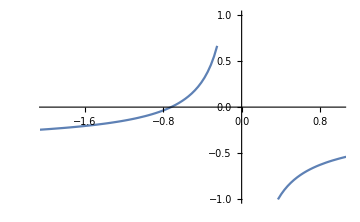

```mathematica
Plot[ptest[Ei]-0.5,{Ei,-5,100},Exclusions->{(ptest[Ei]-ptest[Ei+0.1])/.1==10,(ptest[Ei]-ptest[Ei+0.1])/.1==-10},ImageSize->Medium, PlotRange->{{-2,1},{-1,1}},AxesLabel->MaTeX[{"\\epsilon"," w(x ; \\epsilon)"}, Magnification->1.8],BaseStyle->texStyle]
```

```mathematica
Export["spectrum_all.pdf", Plot[ptest[Ei]-0.5,{Ei,-5,100},Exclusions->{(ptest[Ei]-ptest[Ei+0.1])/.1==10,(ptest[Ei]-ptest[Ei+0.1])/.1==-10},ImageSize->Medium, PlotRange->{{-2,50},{-1,1}},AxesLabel->MaTeX[{"\\epsilon"," w(\\sqrt{2} ; \\epsilon)-1/2"}, Magnification->1.8],BaseStyle->texStyle]]
```

ParametricNDSolveValue::prange: Invalid non-numeric value 0.1+Ei for parameter Ei.

General::stop: Further output of ParametricNDSolveValue::prange will be suppressed during this calculation.

Hold::prange: -- Message text not found -- (Ei) (0.1+Charting`Private`pvar$396599)

ParametricNDSolveValue::berr: The scaled boundary value residual error of 2.33556 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

ParametricNDSolveValue::berr: The scaled boundary value residual error of 9.28686 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

ParametricNDSolveValue::berr: The scaled boundary value residual error of 3.50387 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of ParametricNDSolveValue::berr will be suppressed during this calculation.

spectrum_all.pdf

```mathematica
Export["spectrum_neg.pdf", Plot[ptest[Ei]-0.5,{Ei,-5,100},Exclusions->{(ptest[Ei]-ptest[Ei+0.1])/.1==10,(ptest[Ei]-ptest[Ei+0.1])/.1==-10},ImageSize->Medium, PlotRange->{{-2,1},{-1,1}},AxesLabel->MaTeX[{"\\epsilon"," w(\\sqrt{2} ; \\epsilon)-1/2"}, Magnification->1.8],BaseStyle->texStyle]]
```

ParametricNDSolveValue::prange: Invalid non-numeric value 0.1+Ei for parameter Ei.

General::stop: Further output of ParametricNDSolveValue::prange will be suppressed during this calculation.

Hold::prange: -- Message text not found -- (Ei) (0.1+Charting`Private`pvar$659576)

ParametricNDSolveValue::berr: The scaled boundary value residual error of 2.33556 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

ParametricNDSolveValue::berr: The scaled boundary value residual error of 9.28686 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

ParametricNDSolveValue::berr: The scaled boundary value residual error of 3.50387 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of ParametricNDSolveValue::berr will be suppressed during this calculation.

spectrum_neg.pdf

```mathematica
Needs["PacletManager`"]
PacletInstall["CompoundMatrixMethod","Site"->"http://raw.githubusercontent.com/paclets/Repository/master"]
```

Paclet[CompoundMatrixMethod,0.9,<>]

```mathematica
Needs["CompoundMatrixMethod`"]
Clear[L]
```

```mathematica
sys[L_]=ToMatrixSystem[-ψ''[x]+Uder[s111[x]] ψ[x] ==Ei ψ[x],{ψ[-L]==0,ψ[L]==0},ψ,{x,-L,L},Ei];
sys1[L_]=ToMatrixSystem[-ψ''[x]+Uder1[s1111[x]] ψ[x] ==Ei ψ[x],{ψ[-L]==0,ψ[L]==0},ψ,{x,-L,L},Ei];
sol = Evans[Ei,sys[1.46]];
sol1= Evans[Ei,sys1[1.426]];
```

```mathematica
Export["evans.pdf", Plot[{sol1},{Ei,-0.75,-0.65},ImageSize->Medium,AxesLabel->MaTeX[{"\\epsilon"," \\textrm{Evans Function}"}, Magnification->1.8],PlotLegends->MaTeX[{"\\zeta = 0.1","\\zeta = 0.01"},Magnification->1.8],BaseStyle->texStyle]]
```

InterpolatingFunction::dmval: Input value {-1.426} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

evans.pdf

InterpolatingFunction::dmval: Input value {-1.426} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

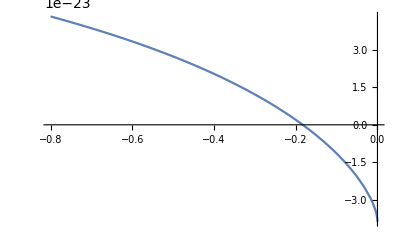

```mathematica
Plot[{sol1},{Ei,-0.8,-0.0}]
```

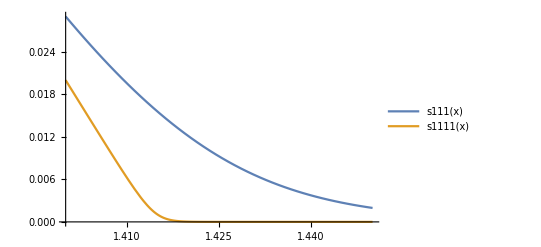

```mathematica
Plot[{s111[x],s1111[x]},{x,1.4,1.45}, PlotLegends->"Expressions"]
```

InterpolatingFunction::dmval: Input value {-1.46} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

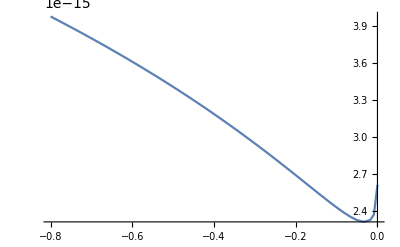

```mathematica
Plot[{sol},{Ei,-0.8,-0.0}]
```

```mathematica
s111[1.42]
```

0.012117

```mathematica
s1111[1.42]
```

0.0000340738

```mathematica
Uder1[s1111[0.75]]
```

-2.08374×10^-9